## Лабораторная работа 6 Робилко Тимур, гр . 221701, Вариант 10

### Задание 1

#### а) Метод Эйлера

```mathematica
Clear[x,y,x0, y0];
f[x_, y_] = y-(3x)/y;
a = 0;
b = 1;
x0= 0;
y0= 1;
```

#### h = 0.1

(0 | 1
0.1 | 1.09136
0.2 | 1.16526
0.3 | 1.22272
0.4 | 1.26343
0.5 | 1.28593
0.6 | 1.28745
0.7 | 1.26347
0.8 | 1.20665
0.9 | 1.10431
1. | 0.931195)

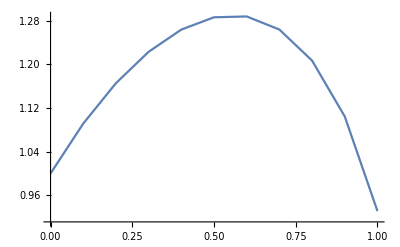

```mathematica
h = 0.1;
n = Floor[(b-a)/h];
x = x0;
y =y0;
Euler1 = Table[{x,y}={x+h, y + h/2(f[x,y]+f[x+h,y+h*f[x,y]])}, {i,n}];
PrependTo[Euler1, {x0, y0}];
Euler1 // MatrixForm
ListLinePlot[Euler1]
```

#### h = 0.05

(0 | 1
0.05 | 1.04768
0.1 | 1.09075
0.15 | 1.12949
0.2 | 1.16405
0.25 | 1.19451
0.3 | 1.22085
0.35 | 1.24298
0.4 | 1.26076
0.45 | 1.27394
0.5 | 1.28222
0.55 | 1.28519
0.6 | 1.28235
0.65 | 1.27302
0.7 | 1.25639
0.75 | 1.23138
0.8 | 1.19659
0.85 | 1.15013
0.9 | 1.08933
0.95 | 1.01023
1. | 0.906405)

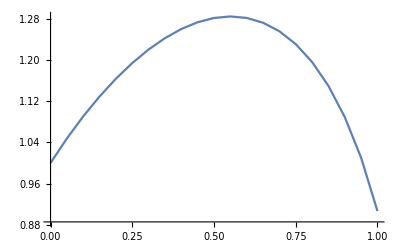

```mathematica
h = 0.05;
n = Floor[(b-a)/h];
x = x0;
y = y0;
Euler2 = Table[{x,y}={x+h, y + h/2(f[x,y]+f[x+h,y+h*f[x,y]])}, {i,n}];
PrependTo[Euler2, {x0, y0}];
Euler2 // MatrixForm
ListLinePlot[Euler2]
```

#### б) Метод Рунге-Кутта 4 порядка

```mathematica
Clear[x,y];
```

#### h = 0.1

(0 | 1
0.1 | 1.09055
0.2 | 1.16365
0.3 | 1.22022
0.4 | 1.25986
0.5 | 1.28096
0.6 | 1.28061
0.7 | 1.25396
0.8 | 1.19311
0.9 | 1.08407
1. | 0.897485)

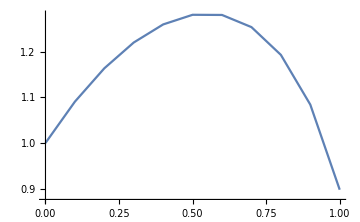

```mathematica
h = 0.1;
x = x0;
y = y0;
n = Floor[(b-a)/h];
RungeKutta1 = List[{x0,y0}];

For[k=1,k≤n,k++,
k1[x_,y_]:=h*f[x,y];
k2[x_,y_]:=h*f[x+h/2,y+k1[x,y]/2];k3[x_,y_]:=h*f[x+h/2,y+k2[x,y]/2];k4[x_,y_]:=h*f[x+h,y+k3[x,y]];y=y+(k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6;x=x+h;RungeKutta1=Append[RungeKutta1,{x,y}]]
RungeKutta1 // MatrixForm
ListLinePlot[RungeKutta1]
```

#### h = 0.05

(0 | 1
0.05 | 1.04758
0.1 | 1.09055
0.15 | 1.12919
0.2 | 1.16365
0.25 | 1.194
0.3 | 1.22022
0.35 | 1.24223
0.4 | 1.25985
0.45 | 1.27287
0.5 | 1.28096
0.55 | 1.28371
0.6 | 1.2806
0.65 | 1.27097
0.7 | 1.25395
0.75 | 1.22848
0.8 | 1.1931
0.85 | 1.14587
0.9 | 1.08406
0.95 | 1.00352
1. | 0.897481)

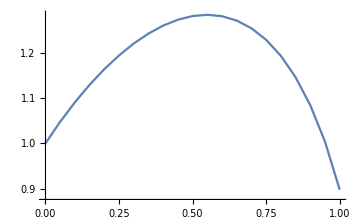

```mathematica
h = 0.05;
x = x0;
y = y0;
n = Floor[(b-a)/h];
RungeKutta2 = List[{x0,y0}];

k1[x_,y_]:=h*f[x,y];
k2[x_,y_]:=h*f[x+h/2,y+k1[x,y]/2];k3[x_,y_]:=h*f[x+h/2,y+k2[x,y]/2];k4[x_,y_]:=h*f[x+h,y+k3[x,y]];

For[k=1,k≤n,k++,
y=y+(k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6;x=x+h;RungeKutta2=Append[RungeKutta2,{x,y}]]

RungeKutta2 // MatrixForm
ListLinePlot[RungeKutta2]
```

#### в) Построение графиков с помощью DSolve и NDSolve

#### DSolve

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

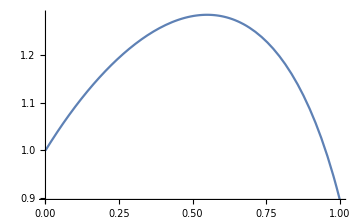

```mathematica
Clear[x,y];
DSolveSoltuion = DSolve[{y'[x]==y[x]-(3x)/y[x], y[x0]==y0}, y[x],x];
DSolveFunctin[x_] = y[x]/.Flatten[DSolveSoltuion];
DSolvePlot = Plot[DSolveFunctin[x], {x,a,b}, ImageSize->Medium]
```

#### NDSolve

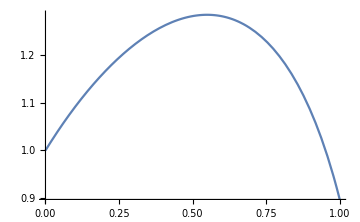

```mathematica
NDSolveSoltuion = NDSolve[{y'[x]==y[x]-(3x)/y[x], y[x0]==y0}, y[x],{x,a,b}];
NDSolveFunctin[x_] = y[x]/.Flatten[NDSolveSoltuion];
NDSolvePlot = Plot[NDSolveFunctin[x], {x,a,b}, ImageSize->Medium]
```

#### Оценка результатов

#### Норма для метода Эйлера (h = 0.1)

```mathematica
d1=Table[DSolveFunctin[x0+(i-1)*h]-Euler1⟦i,2⟧,{i,11}];
Norm[d1]
```

0.439546

#### Норма для метода Эйлера (h = 0.05)

```mathematica
d2=Table[DSolveFunctin[x0+(i-1)*h]-Euler2⟦i,2⟧,{i,21}];
Norm[d2]
```

0.0145552

#### Норма для метода Рунге - Кутта 4-го порядка (h = 0.1)

```mathematica
d3=Table[DSolveFunctin[x0+(i-1)*h]-RungeKutta1⟦i,2⟧,{i,11}];
Norm[d3]
```

0.472476

#### Норма для метода Рунге - Кутта 4-го порядка (h = 0.05)

```mathematica
d4=Table[DSolveFunctin[x0+(i-1)*h]-RungeKutta2⟦i,2⟧,{i,11}];
Norm[d4]
```

4.15543×10^-7

Таким образом, точность метода Рунге - Кутта в сравнении с методом Эйлера проявляется при уменьшении шага, в то время как при большом шаге результаты оказываются сравнивыми.

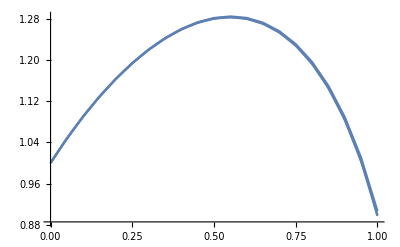

```mathematica
Show[ListLinePlot[Euler2], ListLinePlot[RungeKutta2], DSolvePlot]
```

### Задание 2

#### а) Метод Эйлера

```mathematica
Clear[x,y,z,x0, y0, z0];
x0 = 0;
y0 = 1;
z0 = 0.6;
f[x_,y_,z_] := y^2/z;
g[x_,y_,z_]:=0.5y;
```

#### h = 0.1

(0 | 1
0.1 | 1.16667
0.2 | 1.37607
0.3 | 1.6434
0.4 | 1.99092
0.5 | 2.4522
0.6 | 3.07933
0.7 | 3.95613
0.8 | 5.22297
0.9 | 7.12631
1. | 10.1235)

(0 | 0.6
0.1 | 0.65
0.2 | 0.708333
0.3 | 0.777137
0.4 | 0.859307
0.5 | 0.958853
0.6 | 1.08146
0.7 | 1.23543
0.8 | 1.43323
0.9 | 1.69438
1. | 2.0507)

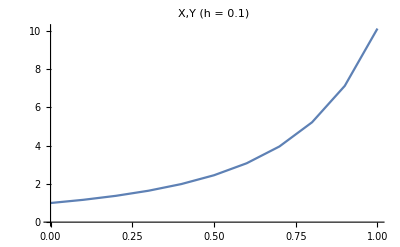

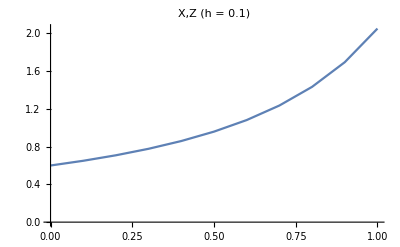

```mathematica
h = 0.1;
n = Floor[(b-a)/h];
x=x0;
y=y0;
z=z0;
Euler21 = Table[{x,y,z} = {x+h, y+h*f[x,y,z], z+h*g[x,y,z]}, {i,n}];
PrependTo[Euler21, {x0,y0,z0}];
Euler21y = Table[{Euler21[[i,1]],Euler21[[i,2]]},{i,n+1}];
Euler21z = Table[{Euler21[[i,1]],Euler21[[i,3]]},{i,n+1}];
Euler21y // MatrixForm
Euler21z // MatrixForm
ListLinePlot[Euler21y, PlotLabel->"X,Y (h = 0.1)"]
ListLinePlot[Euler21z, PlotLabel->"X,Z (h = 0.1)"]
```

#### h = 0.05

(0 | 1
0.05 | 1.08333
0.1 | 1.17722
0.15 | 1.28349
0.2 | 1.40434
0.25 | 1.54253
0.3 | 1.70143
0.35 | 1.88528
0.4 | 2.09945
0.45 | 2.35076
0.5 | 2.64804
0.55 | 3.00283
0.6 | 3.43042
0.65 | 3.95137
0.7 | 4.59377
0.75 | 5.39676
0.8 | 6.41593
0.85 | 7.73211
0.9 | 9.46585
0.95 | 11.8023
1. | 15.0355)

(0 | 0.6
0.05 | 0.625
0.1 | 0.652083
0.15 | 0.681514
0.2 | 0.713601
0.25 | 0.74871
0.3 | 0.787273
0.35 | 0.829809
0.4 | 0.876941
0.45 | 0.929427
0.5 | 0.988196
0.55 | 1.0544
0.6 | 1.12947
0.65 | 1.21523
0.7 | 1.31401
0.75 | 1.42886
0.8 | 1.56378
0.85 | 1.72417
0.9 | 1.91748
0.95 | 2.15412
1. | 2.44918)

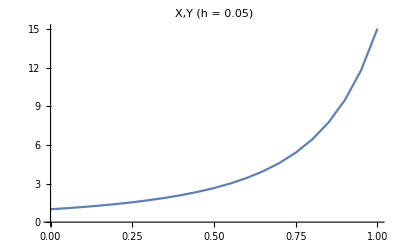

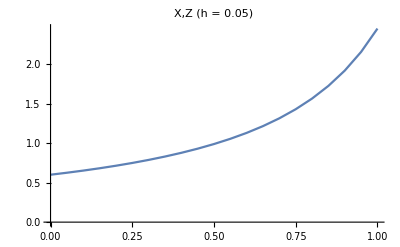

```mathematica
h = 0.05;
n = Floor[(b-a)/h];
x=x0;
y=y0;
z=z0;
Euler22 = Table[{x,y,z} = {x+h, y+h*f[x,y,z], z+h*g[x,y,z]}, {i,n}];
PrependTo[Euler22, {x0,y0,z0}];
Euler22y = Table[{Euler22[[i,1]],Euler22[[i,2]]},{i,n+1}];
Euler22z = Table[{Euler22[[i,1]],Euler22[[i,3]]},{i,n+1}];
Euler22y // MatrixForm
Euler22z // MatrixForm
ListLinePlot[Euler22y, PlotLabel->"X,Y (h = 0.05)"]
ListLinePlot[Euler22z, PlotLabel->"X,Z (h = 0.05)"]
```

#### б) Метод Рунге-Кутта 4-го порядка

```mathematica
Clear[x,y,z,x0, y0, z0];
x0 = 0;
y0 = 1;
z0 = 0.6;
f[x_,y_,z_] := y^2/z;
g[x_,y_,z_]:=0.5*y;
```

#### h = 0.1

(0 | 1
0.1 | 1.19008
0.2 | 1.43998
0.3 | 1.77772
0.4 | 2.24987
0.5 | 2.93845
0.6 | 3.99914
0.7 | 5.7574
0.8 | 8.99046
0.9 | 15.9521
1. | 35.5839)

(0 | 0.6
0.1 | 0.654544
0.2 | 0.719995
0.3 | 0.799989
0.4 | 0.899977
0.5 | 1.02852
0.6 | 1.19988
0.7 | 1.43971
0.8 | 1.79915
0.9 | 2.39686
1. | 3.58208)

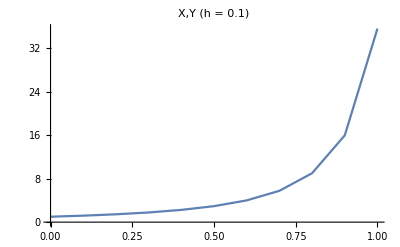

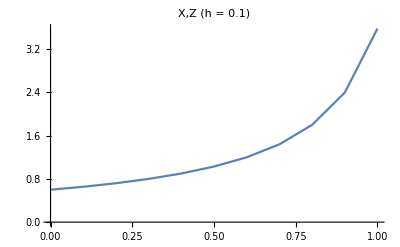

```mathematica
h = 0.1;
n = Floor[(b-a)/h];
x=x0;
y=y0;
z=z0;

RungeKutta21Y=List[{x0,y0}];
RungeKutta21Z=List[{x0,z0}];

k1[x_,y_,z_]:=h*f[x,y,z];
r1[x_,y_,z_]:=h*g[x,y,z];
k2[x_,y_,z_]:=h*f[x+h/2,y+k1[x,y,z]/2,z+r1[x,y,z]/2];r2[x_,y_,z_]:=h*g[x+h/2,y+k1[x,y,z]/2,z+r1[x,y,z]/2];k3[x_,y_,z_]:=h*f[x+h/2,y+k2[x,y,z]/2,z+r2[x,y,z]/2];r3[x_,y_,z_]:=h*g[x+h/2,y+k2[x,y,z]/2,z+r2[x,y,z]/2];k4[x_,y_,z_]:=h*f[x+h,y+k3[x,y,z],z+r3[x,y,z]];r4[x_,y_,z_]:=h*g[x+h,y+k3[x,y,z],z+r3[x,y,z]];

For[k=1,k≤n,k++,
currentY=y;y=y+(k1[x,y,z]+2*k2[x,y,z]+2*k3[x,y,z]+k4[x,y,z])/6;z=z+(r1[x,currentY,z]+2*r2[x,currentY,z]+2*r3[x,currentY,z]+r4[x,currentY,z])/6;x=x+h;RungeKutta21Y=Append[RungeKutta21Y,{x,y}];RungeKutta21Z=Append[RungeKutta21Z,{x,z}];]

RungeKutta21Y // MatrixForm
RungeKutta21Z // MatrixForm

ListLinePlot[RungeKutta21Y, PlotLabel->"X,Y (h = 0.1)"]
ListLinePlot[RungeKutta21Z, PlotLabel->"X,Z (h = 0.1)"]
```

#### h = 0.05

(0 | 1
0.05 | 1.08885
0.1 | 1.19008
0.15 | 1.30612
0.2 | 1.44
0.25 | 1.59557
0.3 | 1.77777
0.35 | 1.99307
0.4 | 2.24999
0.45 | 2.55999
0.5 | 2.93875
0.55 | 3.40825
0.6 | 3.99994
0.65 | 4.76022
0.7 | 5.75981
0.75 | 7.11075
0.8 | 8.99926
0.85 | 11.7535
0.9 | 15.996
0.95 | 23.0287
1. | 35.9601)

(0 | 0.6
0.05 | 0.626087
0.1 | 0.654545
0.15 | 0.685714
0.2 | 0.72
0.25 | 0.757894
0.3 | 0.799999
0.35 | 0.847058
0.4 | 0.899998
0.45 | 0.959998
0.5 | 1.02857
0.55 | 1.10769
0.6 | 1.19999
0.65 | 1.30908
0.7 | 1.43998
0.75 | 1.59996
0.8 | 1.79993
0.85 | 2.05701
0.9 | 2.39973
0.95 | 2.87936
1. | 3.59822)

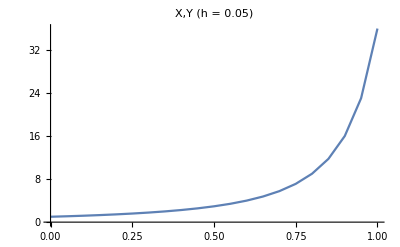

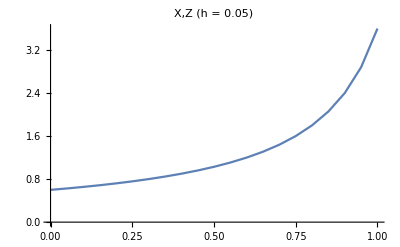

```mathematica
h = 0.05;
n = Floor[(b-a)/h];
x=x0;
y=y0;
z=z0;

RungeKutta22Y = List[{x0,y0}];
RungeKutta22Z = List[{x0,z0}];

For[k=1,k≤n,k++,
currentY=y;y=y+(k1[x,y,z]+2*k2[x,y,z]+2*k3[x,y,z]+k4[x,y,z])/6;z=z+(r1[x,currentY,z]+2*r2[x,currentY,z]+2*r3[x,currentY,z]+r4[x,currentY,z])/6;x=x+h;RungeKutta22Y=Append[RungeKutta22Y,{x,y}];RungeKutta22Z=Append[RungeKutta22Z,{x,z}];]

RungeKutta22Y // MatrixForm
RungeKutta22Z // MatrixForm

ListLinePlot[RungeKutta22Y, PlotLabel->"X,Y (h = 0.05)"]
ListLinePlot[RungeKutta22Z, PlotLabel->"X,Z (h = 0.05)"]
```

#### Построение с помощью DSolve, NDSolve

#### DSolve

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

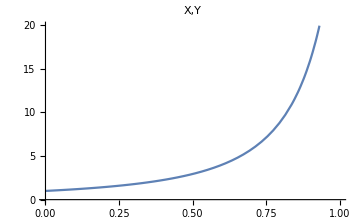

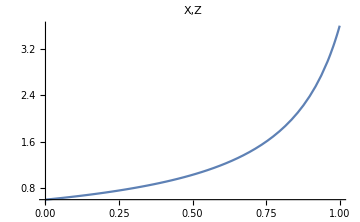

```mathematica
Clear[x,y,z];
DSolveSoltuion2 = DSolve[{y'[x]==y[x]^2/z[x],z '[x]==0.5*y[x], y[x0]==y0, z[x0]==z0}, {y[x], z[x]},x];
DSolveFunction2y[x_] = y[x]/.Flatten[DSolveSoltuion2];
DSolveFunction2z[x_] = z[x]/.Flatten[DSolveSoltuion2];
DSolvePlot2y = Plot[DSolveFunction2y[x], {x,a,b}, PlotLabel->"X,Y"]
DSolvePlot2z = Plot[DSolveFunction2z[x], {x,a,b}, PlotLabel->"X,Z"]
```

#### NDSolve

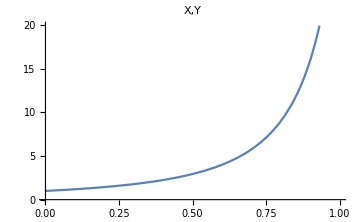

-Graphics-

```mathematica
Clear[x,y,z];
NDSolveSoltuion2 = NDSolve[{y'[x]==y[x]^2/z[x],z '[x]-0.5*y[x] == 0, y[x0]==y0, z[x0]==z0}, {y[x], z[x]},{x,a,b}];
NDSolveFunction2y[x_] = y[x]/.Flatten[NDSolveSoltuion2];
NDSolveFunction2z[x_] = z[x]/.Flatten[NDSolveSoltuion2];
NDSolvePlot2y = Plot[NDSolveFunction2y[x], {x,a,b},PlotLabel->"X,Y"]
NDSolvePlot2z = Plot[NDSolveFunction2z[x], {x,a,b}, PlotLabel->"X,Z"]
```

#### Оценка результатов

#### Норма для метода Эйлера (h = 0.1)

```mathematica
d21y=Table[DSolveFunction2y[x0+(i-1)*h]-Euler21y⟦i,2⟧,{i,11}];
Norm[d21y]
```

9.38348

```mathematica
d21z=Table[DSolveFunction2z[x0+(i-1)*h]-Euler21z⟦i,2⟧,{i,11}];
Norm[d21z]
```

1.47312

#### Норма для метода Эйлера (h = 0.05)

```mathematica
d22y=Table[DSolveFunction2y[x0+(i-1)*h]-Euler22y⟦i,2⟧,{i,21}];
Norm[d22y]
```

25.2382

```mathematica
d22z=Table[DSolveFunction2z[x0+(i-1)*h]-Euler22z⟦i,2⟧,{i,21}];
Norm[d22z]
```

1.52193

#### Норма для метода Рунге-Кутта (h = 0.1)

```mathematica
d23y=Table[DSolveFunction2y[x0+(i-1)*h]-RungeKutta21Y⟦i,2⟧,{i,11}];
Norm[d23y]
```

36.2264

```mathematica
d23z=Table[DSolveFunction2z[x0+(i-1)*h]-RungeKutta21Z⟦i,2⟧,{i,11}];
Norm[d23z]
```

3.16676

#### Норма для метода Рунге-Кутта (h = 0.05)

```mathematica
d24y=Table[DSolveFunction2y[x0+(i-1)*h]-RungeKutta22Y⟦i,2⟧,{i,21}];
Norm[d24y]
```

0.041703

```mathematica
d24z=Table[DSolveFunction2z[x0+(i-1)*h]-RungeKutta22Z⟦i,2⟧,{i,21}];
Norm[d24z]
```

0.00191266

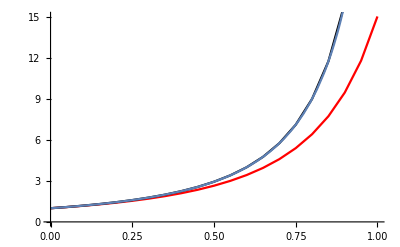

```mathematica
Show[ListLinePlot[Euler22y, PlotStyle->Red], ListLinePlot[RungeKutta22Y, PlotStyle->Black], DSolvePlot2y]
```

Таким образом, метод Эйлера показывает более низкую точность из-за
накопленных ошибок при численном интегрировании. Метод Рунге-Кутта при этом обеспечивает высшую точность даже при значении шага h = 0.1 .